## Visualisation of the average I (deprecated)

```mathematica
SetDirectory["/Users/leonor/Documents/Warwick/PhD Interdisciplinary Mathematics/mpcSim-1.0/velprofile"]
```

/Users/leonor/Documents/Warwick/PhD Interdisciplinary Mathematics/mpcSim-1.0/velprofile

```mathematica
data=Import["velprofile_11.dat"];
nynz=data[[1,2]];nz=data[[1,3]];
```

```mathematica
(* Checking, for peace of mind *)
nynz-(Length[data]-1) ===0
```

True

```mathematica
(*Remove first row from data -info line- *)
data=Delete[data,1];
```

```mathematica
(*Average velocities in each cell *)
vel=Mean/@data;
vel=vel/.Mean[{}]-> 0.0;
```

```mathematica
(*Order cells in 2D as they are in the x-slice*)
vel=Partition[vel,nz];
```

```mathematica
(* Create grid *)
a=1.0; (*This value is unlikely to change, no need to change it in the datafile *)
```

```mathematica
grid=Table[{a/2+k*a,s*a/2},{s,1,nynz/nz},{k,0,nz-1}];
```

```mathematica
(* Checking, extra peace of mind *)
Length[vel]===Length[grid]
```

True

```mathematica
(* Build the data for plotting *)
profiledata={Partition[Flatten[Riffle[grid[[1]],vel[[1]]]],3],Partition[Flatten[Riffle[grid[[2]],vel[[2]]]],3]};
```

```mathematica
For[i=3,i<=Length[grid],i++,profiledata=Append[profiledata,Partition[Flatten[Riffle[grid[[i]],vel[[i]]]],3]]]
```

```mathematica
vel//MatrixForm
```

(0. | 0. | 0. | 0.3494 | -0.070072 | 0.020433 | 0.273639 | -0.135819 | 0.302258 | 0. | 0. | 0.
0. | 0. | -0.0332468 | -0.20132 | 0.154113 | 0.212036 | 0.215114 | 0.122944 | 0.309744 | 0.608662 | 0. | 0.
0. | 0.0643875 | 0.517928 | 0.303628 | 0.0278931 | 0.309539 | 0.389443 | -0.144226 | 0.343749 | 0.00173517 | -0.23619 | 0.
-0.385027 | 0.185564 | -0.0782331 | 0.0293789 | -0.00681019 | 0.446265 | -0.134739 | 0.335143 | -0.156436 | 0.190836 | -0.0147819 | 0.
0.58515 | -0.282903 | 0.0186966 | 0.114455 | 0.308852 | 0.38958 | 0.409626 | 0.264905 | -0.219387 | 0.0451107 | 0.290367 | 0.
0.364518 | -0.0889841 | 0.0564228 | -0.0954231 | 0.0058005 | 0.031709 | -0.186505 | 0.256557 | -0.0846411 | 0.0185484 | -0.170765 | 0.204725
-0.250918 | 0.0989763 | 0.207536 | -0.308024 | -0.106979 | 0.477017 | -0.319961 | 0.289509 | 0.370293 | 0.152349 | 0.0457231 | -1.59477
-0.580834 | 0.226558 | -0.157156 | -0.614317 | 0.268444 | 0.313548 | -0.0520429 | -0.0566657 | 0.0301455 | 0.0480737 | 0.0898218 | 1.21691
-0.879243 | 0.192097 | 0.287135 | -0.112656 | -0.296753 | 0.0828898 | 0.192756 | -0.0949316 | -0.217185 | 0.138776 | -0.414601 | 0.
0. | 0.626613 | 0.141408 | 0.501232 | 0.253965 | 0.238382 | -0.0249166 | 0.134817 | -0.227545 | -0.028893 | 0. | 0.
0. | 0. | -0.604115 | 0.212712 | 0.575779 | 0.022638 | 0.193942 | -0.0860028 | 0.0714105 | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.817553 | -0.0036432 | -0.494093 | 2.02856 | 0. | 0. | 0. | 0.)

```mathematica
data
```

{{},{},{},{1.3505,-0.172494,1.16162,0.146864,1.62292,-0.559012,0.323262,0.085923,0.032479,0.480269,-0.907442,0.627914},{-0.324221,0.180327,-1.2164,1.73009,1.67762,-1.44766,-0.657384,0.249512,-1.25687,0.364271},{1.52621,0.168966,0.138176,0.267663,-0.036344,0.448464,0.502798,0.017238,0.390373,-0.302065,-1.71058,-0.688427,-1.27606,1.34429,1.7464,-1.03268,-1.15705},{1.07289,0.403882,-1.3694,-0.336007,-0.125863,0.136524,0.325301,2.32679,0.285388,-0.70935,0.999866},{0.682703,-0.344491,-0.851726,-0.072391,-0.093192},{0.302258},{},{},{},{},{},{-1.15932,-1.09883,0.099044,0.374016,-0.05207,1.63768},{1.12389,-3.14188,-1.6462,-0.343739,0.909598,-0.307718,0.589295,-1.67645,-0.45639,-0.806999,-0.245505,0.847232,1.41219,-0.073325,0.059172,0.164492,-0.631766,0.064737,0.334295},{1.05299,-0.079289,0.644818,0.86401,0.72874,0.683329,-1.86093,1.35554,-0.425588,-0.27587,-0.773873,0.020101,0.069491},{1.02739,-1.62437,-1.10644,0.448677,-0.53584,0.771425,0.793074,-0.085257,-1.31723,0.198416,-0.332508,0.054215,1.57236,1.16203,1.30251,-0.371334,-1.10036,-0.023721,1.91855,-0.376494,2.60311,-0.313417},{1.79446,0.721374,-1.20972,0.457772,0.715071,0.686808,0.353575,0.095855,0.669047,-1.32889,-0.547385,0.173404},{0.070711,-0.165683,0.771089,0.845929,1.47531,0.753741,-0.371299,1.08491,1.09549,-2.18685,0.619915,-0.796003,-1.21127,0.220699,-0.865279,-1.06213,1.05322,-0.664368,2.16961,-0.37886},{-0.466254,-0.217405,-1.12389,-0.071378,0.885282,0.941431,-0.875723,0.410239,-1.16321,1.33332,1.6046,0.163711,0.270405,0.59919,2.35584},{1.69731,-0.479984},{},{},{},{1.16003,0.28553,-1.10356,-0.084445},{-0.656552,2.63288,-0.49781,0.135798,1.3508,1.00434,-0.619397,0.862126,1.21507,-0.247977},{-0.373101,-0.163022,0.745476,-0.154522,2.06808,1.66999,-0.424826,-0.702268,-0.620571,-0.806609,-1.87545,2.18143,-0.088259,-1.3335,0.530144,2.18461,0.969425,0.340554,0.658297,1.26668},{0.503032,2.56151,1.25755,1.36406,-0.757944,-0.852735,0.501964,-1.61686,-1.30872,-0.989342,-0.137263,-0.151741,1.20347,-0.000972,-0.881699,-0.307023,-0.367398,-0.153531,-0.832246,1.72268,-0.171036},{1.45586,-1.25994,-0.025062,0.242886,0.092934,0.032419,0.319333,-0.094439,1.24766,0.924517,1.29099,0.423839,-0.196705,-0.120751},{2.05486,-1.77637,-0.035018,-0.025077,-0.086979,-0.607366,0.212065,1.32753,1.98472,0.879478,0.356024},{-1.62363,-2.11265,0.296358,0.024658,-0.487283,-0.737206,2.38282,-0.059479,-0.280971,-0.190667,0.998776,0.058574},{-0.016658,0.782045,0.312705,1.17126,1.34482,-0.382451,-1.34385,0.290495,0.75608,0.159938,-0.60991,1.66053},{0.153285,-1.49116,-0.404754,-1.49732,0.6873,0.46257,0.997709,1.83427,-0.242313,0.57823,-0.403524,-1.44267,-0.875332,0.347435,1.16519,-0.487598,0.702117,0.177473,1.09857,0.560247,-1.32618,-0.216107,-0.337516},{2.58145,0.381688,0.457196,-2.0637,-0.258403,-2.51537},{},{0.071902,-0.841955},{-0.740852,0.384479,1.05134,-0.16575,0.357491,-0.12337,1.17677,1.11917,-1.00526,0.867741,-0.027311,1.69107,0.033467,-0.226406,-0.22124,-0.708256,0.134298,-0.257229},{-0.475089,0.421204,-0.011742,0.975242,1.33154,-0.41959,1.11945,-0.807003,-1.05614,-0.079038,-0.73257,0.387525,-1.95738,-1.71502,1.0191,-1.04694,1.99078,0.878806,-0.280477,-0.24983,-0.935742},{-0.341506,-0.479357,-1.60665,0.736137,-0.015338,1.02168,0.055535,-1.13414,1.96533,0.09209},{0.543581,0.75569,0.964954,-1.44699,-0.536937,0.904453,1.35928,0.193152,-0.15492,0.197316,-1.86993,0.404629,-0.015655,-1.66387,-0.208672,0.464956},{1.76642,1.85209,-0.056565,0.627944,-0.425374,-0.411445,-0.396889,0.210385,0.804947,0.25464,1.24435,-1.91365,0.432476,0.084845,1.14108,1.09786,1.27339},{-0.318322,2.19258,0.45647,0.115773,0.576212,0.096154,0.513769,-0.083476,0.536189,-1.64838,0.106331,-2.7449,-2.26612,-0.003403,0.450046},{-0.81741,0.085849,1.19826,-0.564031,0.639004,-0.572396,1.91454,2.26679,1.4939,2.21678,-0.948546,0.585667,-0.900707,-2.90008,1.69216,0.108158,0.340906,0.673951,-1.36958,1.57431,0.32047},{-1.18998,-0.155686,0.53978,1.55719,1.72902,-0.865826,-0.642391,-1.05685,0.669946,0.074105,-0.352284,-0.753286,-0.430952,-2.04308,-0.882638,-0.227315,0.282156,0.335026,0.157311,0.488853,-0.436947,1.18131,-1.57548},{-0.938642,0.696656,-0.157057,1.472,1.1879,1.46736,0.714404,-1.71148,0.826814,-1.24351,-1.14698,0.149174,-0.047524,-0.431376,0.958655,1.39738,0.050435},{0.180838,0.264691,-0.326996,-1.3122,-2.01379,0.286716,0.526908,-0.673462,-0.293376,0.116629,0.971516,-0.011296,1.16543,-0.203221,0.823531,0.261567},{},{1.18924,-0.3825,1.90983,0.019276,1.91684,-0.176701,1.01201,0.657223,0.927842,0.019163,-0.655571},{-1.00577,0.03989,0.700448,0.289856,0.702147,-1.01296,-0.650096,-0.64146,0.277605,-0.368593,-2.09064,-1.21081,1.29264},{0.997254,-1.19459,-1.00768,-1.58789,0.111357,-0.21619,0.320084,-1.35175,-0.574672,1.38033,0.783069,-0.166666,0.606474,1.1407,-1.38522,-0.719936,0.015931,0.777143,0.257909,0.186188,1.52755,1.03581,-0.505182},{0.05963,-0.112112,2.48036,-1.55874,0.575845,1.75681,-1.47679,-0.170566,0.149247,1.62199,-0.502542,0.204323,-0.507372,-1.16033,-0.558391,-0.078403,0.846596,-1.14707,0.491273,1.37534},{2.03266,0.045699,-0.650299,0.066477,0.151541,0.260148,-0.336949,0.266976,0.311231,0.265714,0.984172},{-0.175054,-0.783963,1.26396,0.798366,1.59121,1.45029,-0.088969,0.5476,1.54518,-0.559637,-0.284738,-0.831493,-1.10144,2.08281},{-0.68553,0.420468,0.179433,-0.216886,-0.381436,-0.118009,2.09914,1.12058,0.700361,1.13624,1.2364,-1.09724,0.128005,0.689007,0.933857},{1.63376,0.303001,-0.216379,-0.7172,0.027972,-0.101395,-0.228808,1.79338,1.78095,-0.336654,0.816003,-1.57577},{-1.20157,-2.22269,1.01449,2.17434,0.120882,-1.0037,-0.054747,-0.310835,1.63905,-0.535732,-1.33522,-0.444474,0.026716,-0.309672,-1.01476,2.26192,-2.0611,-0.614917,-0.322309,1.1608,-0.062301,-0.726686,-0.218355,-1.22442},{1.93432,-1.3939,-0.371254,-1.58215,0.010546,1.93246,1.8862,0.225874,0.018392,-0.233675,-0.180562,-0.483423,-0.20707,-0.183817,0.252966,-0.903131},{0.867262,0.975614,0.923579,1.26005,0.573313,-0.048937,1.38175,-1.9679,1.67643,-0.422307,-1.77446,-0.730128,-0.73013,0.402527,0.660886,1.34699,0.541713},{},{-0.775278,0.661261,1.24292,0.490328,-0.370881,0.309161,0.154345,-0.302566,0.792851,1.51224,-0.193308,0.940507,1.05957,0.477731,-0.450818,0.284228},{1.49678,-1.60049,1.26159,2.11399,-1.65682,-0.412355,-0.256833,-0.15766,-0.573187,-0.717908,-0.181424,1.68195,0.471666,-0.852467,-0.733728,-1.30684},{-0.270959,-1.86991,0.458633,0.059937,-0.237204,1.64707,0.710014,0.02479,-0.01457},{-0.650216,-0.410537,-0.303963,1.86912,0.404504,0.236433,-0.312494,1.03287,-0.123871,-1.51378,0.142821,0.731456,-2.34284},{0.457275,0.621632,-0.439552,-1.64302,-0.859831,0.854912,0.158072,-0.416864,-1.17512,-0.471758,2.47592,0.210525,-0.665661,0.055327,-0.579455,0.300277,0.526095,0.695633},{0.796947,-0.750347,0.479017,1.18437,0.542689,0.918841,0.591359,-1.01646,0.281967,-0.864663,0.229904,-2.59835,0.153567,0.495089},{0.02363,-1.40003,2.04472,0.474665,0.57533,-0.322402,-2.20845,-0.589225,-1.04605,-0.575252,-0.051999,1.50965,-0.319733,-1.82279,0.060913,0.662955},{0.272743,-0.602544,0.57485,-0.561668,0.290251,-0.682546,1.50289,-0.875076,-0.417291,1.10082,1.74273,0.143048,0.847044},{-0.966369,-0.413136,-0.967975,1.3735,0.159441,0.478082,-0.803314,-1.79218,0.596595,-1.07574,-0.258602,2.28809,-0.015973,0.212601},{0.967589,0.7973,1.28058,0.67721,0.536657,-1.15542,-1.94163,-0.72518,0.367453,-0.979043,0.166791,0.797727,-1.21592,0.648621,-0.091129,0.165182},{0.957121,-1.09728,0.876915,-1.53459,-0.742899,-0.917754,0.973214,-0.602754,1.18506,0.260759,-0.840502,-0.005186,-0.078538,-0.922241,-0.307493,1.25397,-1.66719,0.135631},{-0.266241,0.675692},{0.252437,1.1699,-0.500013,-1.02525,-1.44566,-0.811596,1.17477,-0.821928},{-0.968764,1.34995,0.730669,0.768377,1.00904,0.035056,1.33626,-0.489643,-0.099738,-0.766586,1.3023,-1.93499,-0.221002,2.70503,-1.0574,0.037957,-1.48022,-0.474727},{-0.907818,0.060562,2.82425,-0.177534,1.69869,0.40381,0.011884,-0.242829,-1.5236,0.02638,-0.040124,1.14653,1.04473,-0.093593,-0.074849,0.665938,-0.852662,-0.234115},{0.378382,-1.04725,0.092114,-0.48626,-1.18803,-0.586021,0.237673,-0.921823,0.288287,-0.383627,-0.191372,-0.107514,2.06882,-2.46571},{-2.17091,-0.697065,0.492963,1.28448,-0.058031,-1.14838,-0.810354,1.18971,0.335308,0.512493},{0.309229,0.756583,1.08779,-0.557065,-0.303055,0.638003,0.222342,1.38576,0.658728,0.434717,0.614159},{1.44489,-0.348636,0.908454,-0.834721,-0.862671,-0.831669,-1.02181,-0.512027,-1.76496,-1.74428,-0.852483,0.659021,0.678297,0.375509,-0.092332},{1.0595,0.080662,-0.768586,-2.06925,-0.394681,0.067953,0.17669,1.78205,0.042632,-0.06819,2.30292,0.791432,0.52309,1.32066,-0.504234},{0.289607,-1.19191,0.973719,-0.569856,-0.086892,1.04663,-0.401634,0.90359,1.17501,0.817534,0.621666,0.447995,0.209295,-0.339405,1.65213,0.377205},{0.815584,-0.863358,1.15007,0.040904,0.031197,2.03631,-2.16002,0.168117},{1.57094,-0.214432,-0.784109,-0.821475,1.36956,1.40643,-1.44103,1.44187,0.513982,-0.324445,-2.12065,-0.04796},{-1.71707,-1.47247},{-0.528225,-0.347953,-0.039426,-1.50722,-0.481352},{0.071402,-0.254333,-0.879124,1.67821,0.296838,0.165335,2.36361,0.797364,-0.126947,0.419646,0.479362,0.572883,-0.529486,-1.02699,0.495417,0.8316,1.88242,-0.550899,-1.42991,0.070939,-0.569629},{2.23225,0.031984,-1.04575,-0.846307,-0.335157,2.69174,0.656998,-2.03818,-0.261994,0.416285,-1.13198,-1.72117,-1.29231,0.443407},{-2.31696,-0.347194,-1.19635,-0.899425,-1.81705,0.089249,-0.189657,0.152452,-0.123725,-0.451145,0.991148,-1.26315},{-0.050427,-0.688402,0.574813,0.656267,-0.047129,-0.503022,0.773517,1.94517,0.973618,-0.561575,1.54487,1.23783,-0.901197,-0.063923,0.841213,-1.43651},{0.67122,0.517067,1.47897,0.05444,1.80725,-0.15737,0.38136,-0.553192,-0.73193,-0.983432,0.964644},{-0.089451,0.321628,-2.00325,1.00069,-1.06378,-0.794106,1.47724,0.083932,1.02025,1.20787,-2.30822,-2.29585,0.246981,-0.047043,0.285461,0.508235,0.038827,1.15162,-0.317498,0.535605},{-0.788199,-0.352975,-0.396819,-0.772462,-0.091405,0.997297,-0.36752,0.878848,0.773473,0.045192,0.592022,0.044659,-0.864945,-0.558383,0.011231},{-0.069423,0.450484,-0.409194,0.358538,0.62418,1.63065,-1.01452,0.035431,-1.45827,1.12826,-0.944524},{-1.10386,0.612787,0.739189,3.00897,2.59287,0.155723,-1.42228,-0.42462,1.345,-0.025529,-0.259489,-0.993929,1.25905,-0.548397,-0.876284,-1.3229,-0.731316,-0.818772,-0.27282},{-0.530062,1.40939,1.43077,0.439428,-0.776328,0.600503,-0.188757,-0.651691,0.352266,-0.202859,-1.14364,0.338849},{0.213128,2.22069},{-1.26274,-0.495746},{1.31607,-0.420194,0.435953,-0.015883,-1.47542,-0.281959,1.09862,0.710001,-0.604738,-0.538549,-0.146304,-0.186867,1.27889,1.49862,-0.143394,0.548709},{1.5987,-0.087476,1.13403,-0.407704,0.406875,1.72139,1.03033,-0.053736,-0.025558,-0.547764,-0.407039,0.196963,0.413981,-0.07915,-1.60157,1.30188},{-1.0508,0.605116,0.961522,-0.82763,-2.6517,0.565705,0.093314,1.40322},{-0.026823,-0.975775,-0.369751,-1.81042,-0.48636,-0.446349,-0.232734,1.35068,-1.84463,-1.23908,1.3231,0.230114,1.31431,0.394011,0.130093,-1.53494,-0.820256},{-0.378871,0.623838,0.134177,1.13368,1.61896,0.361228,0.57233,-0.50691,-0.013221,-1.15789,-1.07474,0.33564,0.508526,1.01814,-0.635105,-1.21354},{0.244743,0.105183,0.592362,-1.39002,1.79124,-0.009982,0.664489,-1.34635,-0.443935,1.71984},{-0.740526,0.322876,1.62802,0.313102,1.0332,-0.000955,-1.68813,-0.692383,-1.02959},{-1.14782,-0.12824,0.637422,-0.311316,-0.407964,-1.18051,-2.13329,-0.402385,0.555389,2.42009,-0.290412},{-0.160998,0.289816,1.87948,-1.4172,-0.799107,2.02088,1.20292,-0.266322,-0.118821,0.401099,-1.50522},{-1.27036,0.088156,0.739232,-0.902611,0.197825,-1.33985},{},{},{-0.187707,1.85413,-1.80299,1.15507,2.11457},{0.167185,-1.16465,-2.19611,0.476338,1.62173,1.98245,-0.735465,-0.154817,0.94136,0.789013,-1.29225,1.61973,0.924036,-0.99886},{-0.74319,1.96115,0.533657,0.664983,-1.54657,0.429171,1.09077,1.20938,-0.270431,1.59389,0.894012,0.04044,-0.317455,1.47743},{0.329211,1.00736,-1.24559,0.063002,0.88325,-0.220165,-0.263977,0.059551,1.24934,-0.270505,0.471722,0.984374},{-1.35067,-0.130748,-1.05292,-1.66673,-0.279729,0.913607,-0.297984,-0.851091,1.27977,0.499967,2.54165,0.928796,1.551,-0.062473,-0.390906,2.18258},{0.092979,1.29604,0.035294,1.37627,-1.88722,0.169949,0.012886,1.47654,0.025257,0.612245,1.2522,-0.193261,-2.49785,2.00759,-1.83095,-0.980853,-1.14473,0.404876,-0.228351,-0.420994,0.360645,-0.486724},{0.536313,1.65803,0.683717,-0.443111,-1.01239,0.502858,-0.614364,-0.603636,-0.001857,0.895462,-0.33657,-0.212323,1.14668,-0.136864,-0.289292,1.10951,-1.24584,0.362701,0.562504},{0.270032,0.118229,-0.673317,-0.448242,0.76709,-0.977007,0.749649,0.410346,0.122819,-1.13485,-0.681651,-0.626378,0.0814,0.238691,-0.555703,-1.30183},{-0.382913,-0.597371,0.536692,-1.13284,2.08986,0.336625,0.462897,-1.06782,0.433205,0.210032,-1.19591,-0.649097,0.319252,-2.38407,2.36319,-1.75757,2.54587,-0.491466,-0.728586,-0.12627,1.34013,-0.759463},{},{},{},{},{-0.604115},{0.741926,-0.339099,0.592651,0.502956,-0.043036,0.495578,0.35115,-0.600426},{1.95153,-0.308923,2.82434,-0.089093,1.35764,0.173126,-0.513449,0.827097,1.47546,-0.028343,-0.181063,-0.018458,0.212433,-2.02027,0.996117,2.94481,0.346035,-0.383735,1.37455},{-0.846083,0.156237,-1.37846,1.17672,1.00472,-0.559907,1.16968,0.315436,0.476953,-1.55989,0.293621},{0.149942,0.371867,-0.145511,0.267808,-1.07339,-0.231928,0.535226,1.51514,0.376784,-0.363663,1.00124,0.364728,-0.247},{-0.453445,0.202447,0.461547,0.158945,-2.39789,0.027555,0.687356,0.112544,0.199741,0.00206,0.116691,-0.834003,0.058578,-1.12569,0.197861,-0.074112,-0.411605,1.52337},{1.77064,-0.489803,1.24525,-2.1167,0.365337,-0.346254},{},{},{},{},{},{},{},{0.052059,-1.68716},{-0.586051,0.543078,-0.589963,0.348943,0.265777},{-0.936559,-0.040203,-0.505516},{2.02856},{},{},{},{}}

```mathematica
(* Render!! *)
ListSurfacePlot3D[profiledata,AxesLabel->{"z","y","vcell"},AxesOrigin->{0,0,0}]
```

-Graphics3D-

## Visualisation of the average II (one run) -Old datafile: first number of each row is not the number of data-

```mathematica
SetDirectory["/Users/leonor/Documents/Warwick/PhD Interdisciplinary Mathematics/mpcSim-1.0/velprofile"];
```

```mathematica
data=Import["velprofile_10.dat"];
nynz=data[[1,2]];nz=data[[1,3]];a=1.0;
(* Checking, for peace of mind *)
nynz-(Length[data]-1) ===0
```

True

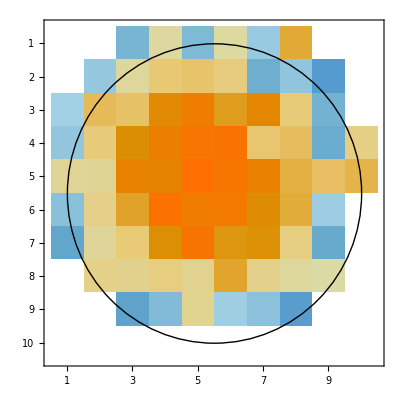

```mathematica
(*Remove first row from data -info line- *)
data=Delete[data,1];
(*Average velocities in each cell *)
vel=Mean/@data;
vel=vel/.Mean[{}]-> 0.0;
vel=Partition[Flatten[vel],nz];
profileplot=MatrixPlot[vel];
Show[{profileplot,Graphics[Circle[{5,5},(nz-a)/2]]}]
```

```mathematica
(* 3D visualisation *)
```

```mathematica
grid=Table[{a/2+α a, a/2 +β a},{α,0,(nynz/nz) -1},{β,0,nz-1}];
(*vel=Partition[vel,nz];*)
profiledata=Table[Partition[Flatten[Riffle[grid[[k]],vel[[k]]]],3],{k,1,nynz/nz}];
profileplot3D=ListSurfacePlot3D[Flatten[profiledata,1],AxesLabel->{"z","y","vcell"},AxesOrigin->{0,0,0},PlotRange->All]
```

-Graphics3D-

```mathematica
Graphics3D[Cylinder[{{nz/2,(nynz/nz)/2,-0.5},{nz/2,(nynz/nz)/2,0.5}},(nz-a)/2],ColorOutput->White];
```

```mathematica
Show[%,profileplot3D]
```

-Graphics3D-

## Doing the average with Mathematica (14 runs) -under construction-

```mathematica
SetDirectory["/Users/leonor/Documents/Warwick/PhD Interdisciplinary Mathematics/mpcSim-1.0/velprofile"];
```

```mathematica
dataarray=Array[data,14]
```

{data[1],data[2],data[3],data[4],data[5],data[6],data[7],data[8],data[9],data[10],data[11],data[12],data[13],data[14]}

```mathematica
Table[data[i]=Import["velprofile_"<>ToString[i]<>".dat"],{i,1,14}];
```

```mathematica
nynz=data[1][[1,2]];nz=data[1][[1,3]];a=1.0;
(* Checking, for peace of mind *)
nynz-(Length[data[1]]-1) ===0
```

True

```mathematica
(*Remove first row from data -info line- *)
Table[data[i]=Delete[data[i],1],{i,1,14}];
```

```mathematica
velocities=Array[vel,nynz];
```

```mathematica
vel[i]=Total[]
```

```mathematica
(*Average velocities in each cell *)
Table[vel[i]=Mean/@data[i],{i,1,14}];
Table[vel[i]=vel[i]/.Mean[{}]-> 0.0,{i,1,14}];
Table[vel[i]=Partition[Flatten[vel[i]],nz],{i,1,14}];
profileplot=MatrixPlot[vel];
Show[{profileplot,Graphics[Circle[{5,5},(nz-a)/2]]}]
```

-Graphics-

```mathematica
(* 3D visualisation *)
```

```mathematica
grid=Table[{a/2+α a, a/2 +β a},{α,0,(nynz/nz) -1},{β,0,nz-1}];
(*vel=Partition[vel,nz];*)
profiledata=Table[Partition[Flatten[Riffle[grid[[k]],vel[[k]]]],3],{k,1,nynz/nz}];
profileplot3D=ListSurfacePlot3D[Flatten[profiledata,1],AxesLabel->{"z","y","vcell"},AxesOrigin->{0,0,0},PlotRange->All]
```

-Graphics3D-

```mathematica
Graphics3D[Cylinder[{{nz/2,(nynz/nz)/2,-0.5},{nz/2,(nynz/nz)/2,0.5}},(nz-a)/2],ColorOutput->White];
```

```mathematica
Show[%,profileplot3D]
```

-Graphics3D-

## Visualisation of the average II (average over several runs)

```mathematica
SetDirectory["/Users/leonor/Documents/Warwick/PhD Interdisciplinary Mathematics/mpcSim-1.0/velprofile"];
```

```mathematica
SetDirectory["/Users/leonor/Dropbox/mpcSim-1.0"]
```

/Users/leonor/Dropbox/mpcSim-1.0

```mathematica
data=Import["vel_CAM_averaged.dat"];
nynz=data[[1,2]];nz=data[[1,3]];a=1.0;
(* Checking, for peace of mind *)
nynz-(Length[data]-1) ===0
```

True

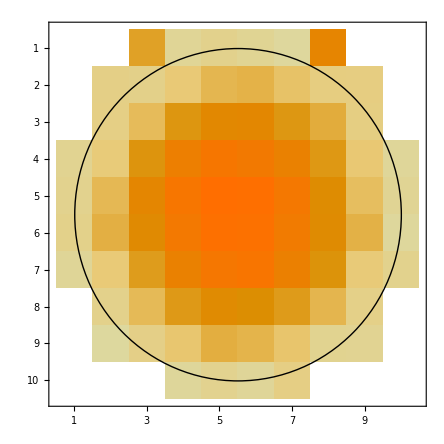

```mathematica
(*Remove first row from data -info line- *)
data=Delete[data,1];
(*Order cells in 2D as they are in the x-slice*)
vel=Partition[Flatten[data],nz];
profileplot=MatrixPlot[vel];
Show[{profileplot,Graphics[Circle[{5,5},(nz-a)/2]]}]
```

```mathematica
vel//MatrixForm
```

(0. | 0. | 1.99955 | 0.511211 | 0.591277 | 0.556421 | 0.439933 | 2.7699 | 0. | 0.
0. | 0.654348 | 0.631869 | 1.05129 | 1.45069 | 1.48941 | 1.1821 | 0.728336 | 0.71567 | 0.
0. | 0.656758 | 1.37571 | 2.20615 | 2.60518 | 2.64889 | 2.19649 | 1.57017 | 0.699006 | 0.
0.572926 | 1.01613 | 2.21714 | 3.04944 | 3.41723 | 3.35755 | 2.97084 | 2.19503 | 1.06736 | 0.475991
0.586553 | 1.40731 | 2.67276 | 3.42607 | 3.78243 | 3.77651 | 3.36678 | 2.48511 | 1.31605 | 0.551748
0.604466 | 1.51528 | 2.53987 | 3.35777 | 3.70062 | 3.69883 | 3.2864 | 2.51028 | 1.49275 | 0.443693
0.510219 | 1.04296 | 2.16058 | 2.96543 | 3.38189 | 3.45122 | 2.98016 | 2.22691 | 1.02152 | 0.590606
0. | 0.592286 | 1.40109 | 2.17697 | 2.53173 | 2.42025 | 2.17314 | 1.45714 | 0.640817 | 0.
0. | 0.384834 | 0.644609 | 1.09601 | 1.52162 | 1.46769 | 1.12537 | 0.581764 | 0.572345 | 0.
0. | 0. | 0. | 0.465448 | 0.586419 | 0.49076 | 0.658015 | 0. | 0. | 0.)

```mathematica
(* 3D visualisation *)
```

```mathematica
grid=Table[{a/2+α a, a/2 +β a},{α,0,(nynz/nz) -1},{β,0,nz-1}];
(*vel=Partition[vel,nz];*)
profiledata=Table[Partition[Flatten[Riffle[grid[[k]],vel[[k]]]],3],{k,1,nynz/nz}];
profileplot3D=ListSurfacePlot3D[Flatten[profiledata,1],AxesLabel->{"z","y","vcell"},AxesOrigin->{0,0,0},PlotRange->All]
```

-Graphics3D-

```mathematica
cylinder=Graphics3D[Cylinder[{{nz/2,(nynz/nz)/2,-1},{nz/2,(nynz/nz)/2,1}},(nz-a)/2],ColorOutput->White];
```

```mathematica
Show[cylinder,profileplot3D]
```

-Graphics3D-

## Visualisation test

```mathematica
nynz=16;nz=4;
```

```mathematica
grid=Table[{a/2+α a, a/2 +β a},{α,0,(nynz/nz) -1},{β,0,nz-1}];
```

```mathematica
grid//MatrixForm
```

((0.5
0.5) | (0.5
1.5) | (0.5
2.5) | (0.5
3.5)
(1.5
0.5) | (1.5
1.5) | (1.5
2.5) | (1.5
3.5)
(2.5
0.5) | (2.5
1.5) | (2.5
2.5) | (2.5
3.5)
(3.5
0.5) | (3.5
1.5) | (3.5
2.5) | (3.5
3.5))

```mathematica
(*vel={0.2,0.5,0.6,0.2,0.2,0.8,0.9,0.3,0.1,0.4,0.6,0.2,0,0.3,0.2,0};*)
vel={1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4};
vel=Partition[vel,nz];
profiledata={Partition[Flatten[Riffle[grid[[1]],vel[[1]]]],3],Partition[Flatten[Riffle[grid[[2]],vel[[2]]]],3]}
```

{{{0.5,0.5,1},{0.5,1.5,1},{0.5,2.5,1},{0.5,3.5,1}},{{1.5,0.5,2},{1.5,1.5,2},{1.5,2.5,2},{1.5,3.5,2}}}

```mathematica
MatrixForm[profiledata]
```

((0.5
0.5
1) | (0.5
1.5
1) | (0.5
2.5
1) | (0.5
3.5
1)
(1.5
0.5
2) | (1.5
1.5
2) | (1.5
2.5
2) | (1.5
3.5
2))

```mathematica
profiledata=Table[Partition[Flatten[Riffle[grid[[k]],vel[[k]]]],3],{k,1,nynz/nz}]
```

{{{0.5,0.5,1},{0.5,1.5,1},{0.5,2.5,1},{0.5,3.5,1}},{{1.5,0.5,2},{1.5,1.5,2},{1.5,2.5,2},{1.5,3.5,2}},{{2.5,0.5,3},{2.5,1.5,3},{2.5,2.5,3},{2.5,3.5,3}},{{3.5,0.5,4},{3.5,1.5,4},{3.5,2.5,4},{3.5,3.5,4}}}

```mathematica
MatrixForm[profiledata]
```

((0.5
0.5
1) | (0.5
1.5
1) | (0.5
2.5
1) | (0.5
3.5
1)
(1.5
0.5
2) | (1.5
1.5
2) | (1.5
2.5
2) | (1.5
3.5
2)
(2.5
0.5
3) | (2.5
1.5
3) | (2.5
2.5
3) | (2.5
3.5
3)
(3.5
0.5
4) | (3.5
1.5
4) | (3.5
2.5
4) | (3.5
3.5
4))

```mathematica
ListSurfacePlot3D[Flatten[profiledata,1],AxesLabel->{"z","y","vcell"},AxesOrigin->{0,0,0},PlotRange->All]
```

-Graphics3D-